```mathematica
(* Sergio Maldonado, written in Wolfram Mahtematica 11.2.0.0 *)
```

This notebook supplements the paper by Maldonado ‘Do equilibrium beach profiles under non-breaking waves minimize energy dissipation?’ (under review). The sections below correspond to the sections in the aforementioned manuscript.
This notebook may be used to generate any solution presented in the manuscript (see NOTES for necessary modifications).

### Section 3

Eq. (8) is obtained directly :

```mathematica
Integrate[√((h^m α)/(1-h^m α)),h,Assumptions->{h>0,m>0,α ∈ Reals} ]
```

(2 h √((h^m α)/(1-h^m α)) √(1-h^m α) Hypergeometric2F1[1/2,1/2+1/m,3/2+1/m,h^m α])/(2+m)

### Section 4

Values of the constants α and β are found numerically by complying with the boundary conditions.

#### Eq. (11)

For example, take the first two terms of eq. (11) (the ' high-order' solution; see note at the end of this section). The following boundary conditions are taken from the measured/digitised profile J & I f :

```mathematica
x0=213.28;
h0=2.79;
x1=1005.22;
h1=11.33;
xl = x1-x0;
ntau=2;
m=3 (ntau+1)/2;
Clear[α,β]
```

Then, a system of two simultaneous equations is solved for:
h = h0 at x = 0; and
h  =h1 at x = x1
(where the shift in x is done only for simplicity)

```mathematica
sol = NSolve[{(2 h0 √(h0^m α))/(2+m)(1 + (Pochhammer[1/2,1] Pochhammer[1/2 + 1/m,1])/Pochhammer[3/2 + 1/m,1] h0^m α)+β==0,(2 h1 √(h1^m α))/(2+m)(1 + (Pochhammer[1/2,1] Pochhammer[1/2 + 1/m,1])/Pochhammer[3/2 + 1/m,1] h1^m α)+β==xl},{α,β},Reals]
{α1,β1}={α,β}/.sol[[1]];
```

{{α→0.00184552,β→-0.385544}}

Plotting the data for reference:

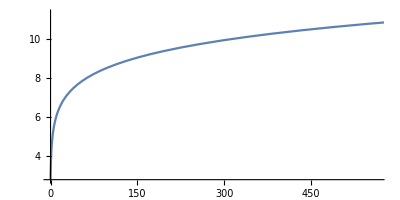

```mathematica
fx[h_] := (2 h √(h^m α1))/(2+m)(1 + (Pochhammer[1/2,1] Pochhammer[1/2 + 1/m,1])/Pochhammer[3/2 + 1/m,1] h^m α1)+β1;
ParametricPlot[{fx[h],h},{h,h0,h1},AspectRatio->1/2]
```

And exporting the data for post-processing if need be:

```mathematica
SetDirectory[NotebookDirectory[]];
th =Table[h,{h,h0,h1,.01}];
tx =Table[fx[h]+x0,{h,h0,h1,.01}];
fileout = "eq_11_high_order.dat";
Export[fileout,{tx,th},"Table"]
```

NOTE:
For the ‘low-order’ solution repeat the procedure above by removing the second term in the series. (Similarly, for higher-order solutions include higher-order terms.)

### Appendix C

#### Eq. (C1)

For eq. (C1), we expand the integrand in power series around h_i:

```mathematica
FullSimplify[Series[√((h^m α)/(1-h^m α)),{h,hi,2}]]
```

√((hi^m α)/(1-hi^m α))+(m √(-(hi^m α)/(-1+hi^m α)) (h-hi))/(2 hi-2 hi^(1+m) α)+(m √((hi^m α)/(1-hi^m α)) (-2+m+2 hi^m (1+m) α) (h-hi)^2)/(8 hi^2 (-1+hi^m α)^2)+O[h-hi]^3

Then, take say the first three terms of the above series and integrate leading to a polynomial of degree 3.

```mathematica
Clear[m]
Integrate[√((hi^m α)/(1-hi^m α))+(m √(-(hi^m α)/(-1+hi^m α)) (h-hi))/(2 hi-2 hi^(1+m) α)+(m √((hi^m α)/(1-hi^m α)) (-2+m+2 hi^m (1+m) α) (h-hi)^2)/(8 hi^2 (-1+hi^m α)^2),h]
```

1/(8 hi^2 (-1+hi^m α)^2)√((hi^m α)/(1-hi^m α)) (-h^2 hi (-4+m) m+1/3 h^3 (-2+m) m+h hi^2 (8-6 m+m^2)+2/3 h^3 hi^m m (1+m) α-2 h^2 hi^(1+m) m (2+m) α+2 h hi^(2+m) (-8+3 m+m^2) α+8 h hi^(2+2 m) α^2)

Using again profile J&I f (the boundary conditions of which are given above), we solve the simultaneous system of equations in the same manner as with eq. (11):

```mathematica
ntau=2;
m=3 (ntau+1)/2;
hi = h0;
Clear[α,β]

sol=NSolve[{1/(8 hi^2 (-1+hi^m α)^2)√((hi^m α)/(1-hi^m α)) (-h0^2 hi (-4+m) m+1/3 h0^3 (-2+m) m+h0 hi^2 (8-6 m+m^2)+2/3 h0^3 hi^m m (1+m) α-2 h0^2 hi^(1+m) m (2+m) α+2 h0 hi^(2+m) (-8+3 m+m^2) α+8 h0 hi^(2+2 m) α^2)+β==0,1/(8 hi^2 (-1+hi^m α)^2)√((hi^m α)/(1-hi^m α)) (-hinf^2 hi (-4+m) m+1/3 hinf^3 (-2+m) m+hinf hi^2 (8-6 m+m^2)+2/3 hinf^3 hi^m m (1+m) α-2 hinf^2 hi^(1+m) m (2+m) α+2 hinf hi^(2+m) (-8+3 m+m^2) α+8 hinf hi^(2+2 m) α^2)+β==xl},{α,β},Reals]

{α1,β1}={α,β}/.sol[[1]];
```

{{α→0.00545127,β→-20.0737}}

Plotting for reference:

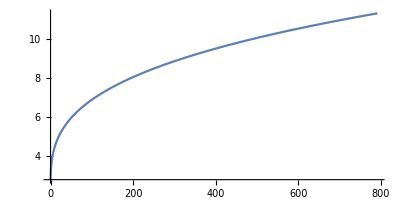

```mathematica
fx[h_] :=1/(8 hi^2 (-1+hi^m α1)^2)√((hi^m α1)/(1-hi^m α1)) (-h^2 hi (-4+m) m+1/3 h^3 (-2+m) m+h hi^2 (8-6 m+m^2)+2/3 h^3 hi^m m (1+m) α1-2 h^2 hi^(1+m) m (2+m) α1+2 h hi^(2+m) (-8+3 m+m^2) α1+8 h hi^(2+2 m) α1^2)+β1;
ParametricPlot[{fx[h],h},{h,h0,h1},AspectRatio->1/2]
```

And export the data for post - processing if need be :

```mathematica
th =Table[h,{h,h0,h1,.01}];
tx =Table[fx[h]+x0,{h,h0,h1,.01}];
fileout = "eq_13_high_order.dat";
Export[fileout,{tx,th},"Table"]
```

NOTE:
For lower-order solutions (such as eq. C1) repeat the procedure above by removing the quadratic term in the series. (For higher-order solutions include higher-order terms.)